```mathematica
Take[deps2,-10]
```

{{16554,130486,{2,9<->13}},{16554,130487,{2,8<->13}},{16597,130507,{2,1<->7}},{16597,130508,{2,5<->7}},{16597,130509,{2,3<->8}},{16597,130510,{2,5<->8}},{16597,130511,{2,6<->10}},{16597,130512,{2,4<->10}},{16597,130513,{2,4<->12}},{16597,130514,{2,6<->13}}}

```mathematica
Take[
Table[
Select[
Map[{#[[1]],#[[2]],Chrom[#[[1]]],Chrom[#[[2]]],#[[3]]}&,
Select[deps2,k[[1]]<= #[[1]]≤k[[2]] && #[[2]]<255000&]
],
#[[3]]<#[[4]]&
]
,{k,mpgBounds}]
,
5
]
```

{{{2,4,24,96,{2,3<->4}}},{{3,6,24,96,{2,2<->5}},{3,7,24,120,{2,3<->5}}},{{5,11,24,120,{2,3<->5}},{5,14,24,96,{2,3<->6}},{5,15,24,96,{2,4<->6}},{7,21,120,288,{2,1<->5}}},{{10,25,24,96,{2,3<->6}},{10,26,24,120,{2,2<->5}},{10,30,24,96,{2,2<->7}},{10,31,24,120,{2,5<->7}},{20,38,96,216,{2,3<->5}},{20,39,96,120,{2,4<->5}},{20,42,96,120,{2,5<->6}},{11,46,120,288,{2,2<->6}},{11,48,120,144,{2,2<->7}},{12,53,24,96,{2,2<->5}},{13,60,24,96,{2,2<->7}},{14,65,96,384,{2,3<->4}},{17,72,24,504,{2,3<->4}},{18,72,72,504,{2,2<->6}},{19,72,96,504,{2,2<->6}},{21,72,288,504,{2,1<->5}}},{{24,76,24,120,{2,5<->6}},{24,78,24,96,{2,2<->7}},{24,79,24,96,{2,2<->5}},{24,80,24,288,{2,5<->7}},{24,82,24,96,{2,3<->9}},{41,95,96,264,{2,3<->5}},{41,96,96,120,{2,4<->5}},{41,98,96,120,{2,1<->7}},{41,102,96,384,{2,5<->8}},{25,118,96,384,{2,2<->7}},{25,120,96,120,{2,2<->9}},{27,129,24,120,{2,2<->6}},{27,131,24,96,{2,2<->7}},{27,132,24,120,{2,5<->7}},{49,144,120,288,{2,4<->6}},{49,146,120,144,{2,2<->7}},{26,158,120,480,{2,2<->7}},{26,159,120,288,{2,2<->5}},{28,167,24,96,{2,2<->7}},{39,178,120,168,{2,3<->4}},{39,181,120,288,{2,6<->7}},{53,186,96,120,{2,2<->6}},{53,187,96,216,{2,3<->6}},{29,199,24,96,{2,2<->6}},{29,201,24,120,{2,3<->5}},{29,203,24,96,{2,5<->8}},{37,211,96,120,{2,2<->6}},{66,219,96,120,{2,3<->4}},{30,227,96,120,{2,2<->6}},{30,228,96,384,{2,3<->5}},{30,229,96,384,{2,4<->8}},{46,231,288,504,{2,3<->4}},{36,261,72,192,{2,2<->6}},{38,262,216,672,{2,2<->6}},{58,293,24,96,{2,2<->7}},{70,304,24,96,{2,3<->4}},{71,304,24,96,{2,3<->4}},{71,305,24,1056,{2,2<->6}},{72,305,504,1056,{2,1<->5}}}}

```mathematica
PaintGraph2[g_,pre_, opts__]:=Block[{sols},
sols=ToVars2[g,pre];
Map[
Graph[g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#],  VertexSize->Medium]&
,sols]
]
```

```mathematica
ToVars2[g_, pre_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
(* works only for graphs in which 1,2 and 3 are connected *)
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> pre;(* "x1 == 1 && x2== 2 && x3==3";*)
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
Take[deps2,3]
```

{{1,2,{2,1<->4}},{1,3,{2,2<->4}},{2,3,{2,2<->4}}}

```mathematica
Take[
Table[
Select[
Map[{#[[1]],#[[2]],Chrom[#[[1]]],Chrom[#[[2]]],#[[3]]}&,
Select[deps2,k[[1]]<= #[[1]]≤k[[2]] && #[[2]]<255000&]
],
#[[3]]>#[[4]]&
]
,{k,mpgBounds}]
,
5
]
```

{{},{{4,10,96,24,{2,2<->4}}},{{7,22,120,24,{2,3<->6}}},{{20,40,96,72,{2,3<->6}},{21,73,288,24,{2,4<->5}}},{{41,97,96,72,{2,3<->6}},{41,99,96,72,{2,1<->5}},{25,114,96,72,{2,2<->5}},{25,119,96,72,{2,5<->7}},{49,142,120,72,{2,2<->6}},{49,143,120,72,{2,3<->4}},{26,160,120,72,{2,5<->8}},{39,180,120,72,{2,3<->6}},{35,237,96,24,{2,2<->6}},{38,263,216,144,{2,1<->5}},{40,264,72,48,{2,3<->4}},{42,265,120,96,{2,3<->4}},{45,267,120,24,{2,4<->5}},{48,267,144,24,{2,2<->6}},{50,267,48,24,{2,2<->6}},{60,299,96,24,{2,3<->4}},{65,303,384,24,{2,3<->4}},{72,306,504,24,{2,3<->7}}}}

```mathematica
ChromaticPolynomial[Rule2[ReadGrof[7],3<->6,2<->4],4]
```

72

```mathematica
ChromaticPolynomial[ReadGrof[7],4]
```

120

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[7],3<->6,2<->4],ReadGrof[22]]
```

False

```mathematica
PaintGraph2[VertexDelete[ReadGrof[25],4],"x2==1&&x5==2&&x6==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{2<->5}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[25],"x2==1&&x5==2&&x6==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{2<->5}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[7],"x3==1&&x6==2&&x2==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->6}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Chrom[7]
```

120

```mathematica
PaintGraph2[VertexDelete[ReadGrof[41],8],"x3==1&&x6==2&&x2==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->6,1<->5}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[VertexDelete[ReadGrof[42],8],"x3==1&&x4==2&&x6==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->4}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[42],"x3==1&&x4==2&&x6==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->4}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

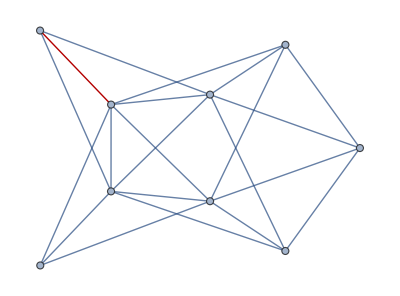

```mathematica
Graph[ReadGrof[42],GraphHighlight->{4<->5}]
```

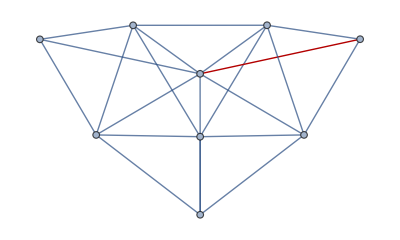

```mathematica
Graph[ReadGrof[45],GraphHighlight->{4<->5}]
```

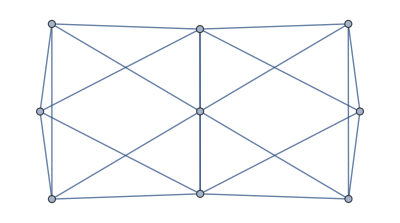

```mathematica
ReadGrof[65]
```

```mathematica
PaintGraph2[ReadGrof[65],"x3==1&&x4==2&&x8==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->4}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[72],"x3==1&&x7==2&&x1==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->7}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[4],"x2==1&&x4==2&&x6==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{2<->4}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

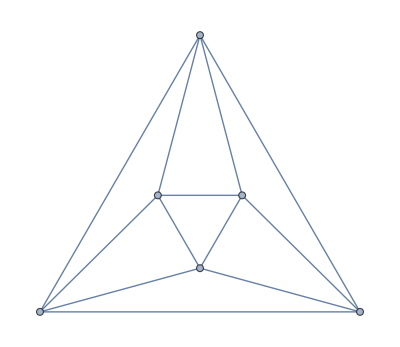

```mathematica
GraphData["OctahedralGraph"]
```

```mathematica
EdgeList[ReadGrof[4]]
```

{1<->2,1<->3,1<->5,1<->6,2<->3,2<->4,2<->6,3<->4,3<->5,4<->5,4<->6,5<->6}

```mathematica
PaintGraph2[ReadGrof[7],"x3==1&&x6==2&&x4==3",  GraphLayout->"PlanarEmbedding",VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->6}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[20],"x3==1&&x6==2&&x4==3",  GraphLayout->"PlanarEmbedding",VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->6}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[VertexDelete[ ReadGrof[20],{8,4}],"x3==1&&x6==2&&x2==3",  GraphLayout->"PlanarEmbedding",VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->6}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[VertexDelete[ ReadGrof[20],{8}],"x3==1&&x6==2&&x2==3",  GraphLayout->"PlanarEmbedding",VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{3<->6}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
IsomorphicGraphQ[VertexDelete[ ReadGrof[20],{8,4}],ReadGrof[4]]
```

True

```mathematica
ChromaticPolynomial[ReadGrof[21],4]
```

288

```mathematica
ChromaticPolynomial[EdgeAdd[VertexAdd[EdgeDelete[ReadGrof[21],{4<->5}],100],{5<->100,100<->4,7<->100,6<->100}],4]
```

216

```mathematica
IsomorphicGraphQ[ReadGrof[73],EdgeAdd[VertexAdd[EdgeDelete[ReadGrof[21],{4<->5}],100],{5<->100,100<->4,7<->100,6<->100}]]
```

False

```mathematica
PaintGraph2[ReadGrof[21],"x4==1&&x5==2&&x7==3",  GraphLayout->"PlanarEmbedding",VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{4<->5}, ImageSize->300]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph2[ReadGrof[10],"x2==1&&x4==2&&x6==3", GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlightStyle->"Dashed", GraphHighlight->{2<->4}]
```

{-Graphics-}

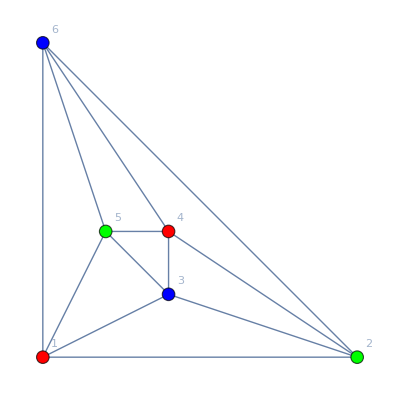
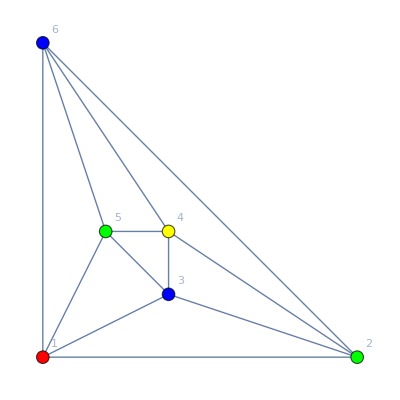
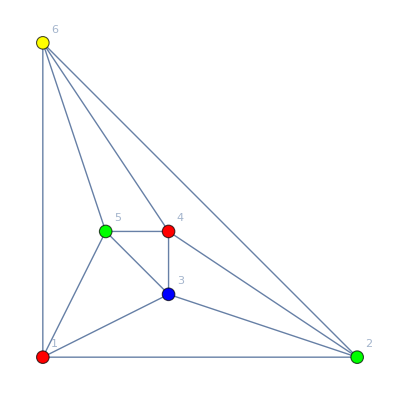
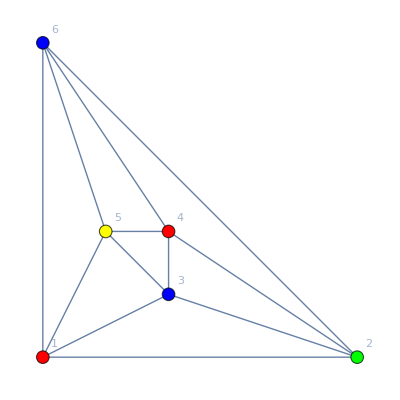

```mathematica
PaintGraph2[ReadGrof[4], GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

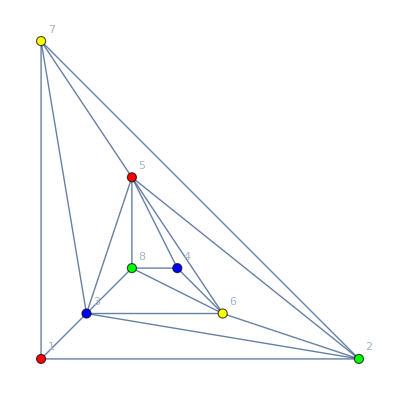

```mathematica
PaintGraph2[ReadGrof[10], GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

```mathematica
mpgBounds
```

{{1,2},{3,4},{5,9},{10,23},{24,73},{74,306},{307,1555},{1556,9150},{9151,58716}}

```mathematica
Table[
Select[deps2,k[[1]]<= #[[1]]≤k[[2]]&]
,{k,Most[mpgBounds]}]
```

{{{1,2,{2,1<->4}},{1,3,{2,2<->4}},{2,3,{2,2<->4}},{2,4,{2,3<->4}},{2,5,{2,4<->5}}},6,{{1556,9151,{2,3<->5}},{1556,9152,{2,3<->7}},{1556,9153,{2,5<->7}},{1556,9154,{2,3<->8}},{1556,9155,{2,5<->8}},{1556,9156,{2,3<->6}},{1556,9157,{2,6<->8}},{1556,9158,{2,4<->6}},{1556,9159,{2,4<->8}},{1556,9160,{2,2<->9}},{1556,9161,{2,3<->9}},5832,{2744,24842,{2,10<->11}},{2744,24843,{2,7<->12}},{2744,24844,{2,5<->12}},{2766,24860,{2,1<->7}},{2766,24861,{2,3<->5}},{2766,24862,{2,5<->8}},{2766,24863,{2,3<->9}},{2766,24864,{2,6<->9}},{2766,24865,{2,6<->10}},{2766,24866,{2,5<->10}}}}
 |  |  |  |

```mathematica
{{},{{4,"{2,3<->4}"}},{{7,"{2,2<->5}"}},{{16,"{2,3<->6}"},{17,"{2,4<->6}"}},{{26,"{2,3<->6}"},{31,"{2,2<->7}"},{47,"{2,2<->5}"},{52,"{2,2<->7}"},{70,"{2,2<->7}"},{71,"{2,2<->5}"}}}
```

2<->7

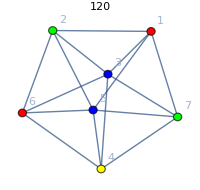
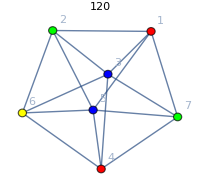
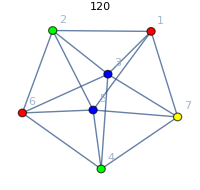
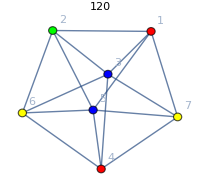
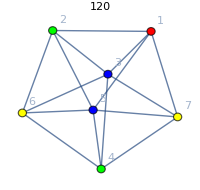

```mathematica
Read[StringToStream["{2,2<->7}"],Expression][[2]]
```

```mathematica
Table[Map[PaintGraph2[ReadGrof[#[[1]]],
GraphLayout->"SpringElectricalEmbedding",
GraphHighlightStyle->"Dashed",
ImageSize->200,
GraphHighlight->{Read[StringToStream[#[[2]]],Expression][[2]]},
 VertexLabels->"Name",
PlotLabel->ChromaticPolynomial[ReadGrof[#[[1]]],4]]&,k],{k,{{{4,"{2,3<->4}"}},{{7,"{2,2<->5}"}},{{16,"{2,3<->6}"},{17,"{2,4<->6}"}},{{26,"{2,3<->6}"},{31,"{2,2<->7}"},{47,"{2,2<->5}"},{52,"{2,2<->7}"},{70,"{2,2<->7}"},{71,"{2,2<->5}"}}}}]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-},{-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}}